```mathematica
(*Decimal number x with n decimal places:
N[x, n]*)
```

```mathematica
N[1/5, 15]
```

0.2

```mathematica
(*Declare a variable*)
```

```mathematica
a = 1
```

```mathematica
(*Define a function f with variable x and rule y:
f[x_] = y*)
```

```mathematica
f[x_] = x^2 - 1
```

-1+x^2

```mathematica
(*Plot a function f with respect to x where x is between a and b:
Plot[f[x], {x, a, b}]*)
```

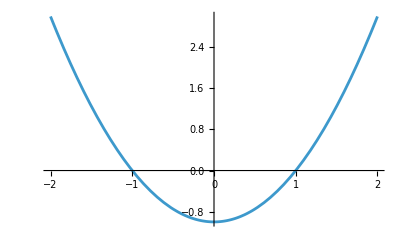

```mathematica
Plot[f[x], {x, -2, 2}]
```

```mathematica
(*Define a multivariable function:
r[v1_, v2_, ...] = y*)
```

```mathematica
r[x_, t_] = x + t^2 - 3
```

-3+t^2+x

```mathematica
(*Plot a multivariable function r with respect to v1 and v2 where v1 is between a and b and v2 is between c and d:
Plot3D[r[v1, v2], {v1, a, b}, {v2, c, d}]*)
```

```mathematica
Plot3D[r[x, t], {x, -1, 1}, {t, 0, 2}]
```

-Graphics3D-

```mathematica
(*Square root of x:
Sqrt[x]*)
```

```mathematica
Sqrt[4]
```

2

```mathematica
(*Euler's number:
E*)
```

```mathematica
E^2
```

ⅇ^2

```mathematica
(*Exponential function of x:
Exp[x]*)
```

```mathematica
Exp[x]
```

ⅇ^x

```mathematica
(*Natural logarithm of x:
Log[x]*)
```

```mathematica
Log[E]
```

1

```mathematica
(*Logarithm base a of x:
Log[x, a]*)
```

```mathematica
Log[10, 10]
```

1

```mathematica
Log[10, 1]
```

0

```mathematica
Log[2, 4]
```

2

```mathematica
(*Hyperbolic sine of x:
Sinh[x]*)
```

```mathematica
Sinh[x]
```

Sinh[x]

```mathematica
(*Power n of x:
Power[x, n]*)
```

```mathematica
Power[2, 10]
```

1024

```mathematica
(*Floor and ceiling of x:
Floor[x], Ceiling[x]*)
```

```mathematica
Floor[2.34]
```

2

```mathematica
Ceiling[2.34]
```

3

```mathematica
(*Absolute value of x:
Abs[x]*)
```

```mathematica
Abs[-43]
```

43

```mathematica
(*Complex number a+bi:
a + bI*)
```

```mathematica
2 + 3I
```

2+3 ⅈ

```mathematica
Abs[2+3I]
```

√13

```mathematica
(*Sign of x (-1 for negative, +1 for positive, and 0 for 0):
Sign[x]*)
```

```mathematica
Sign[-4]
```

-1

```mathematica
(*Round x to the nearest multiple of a:
Round[x, a]*)
```

```mathematica
Round[3.4]
```

3

```mathematica
Round[3.4, 2]
```

4

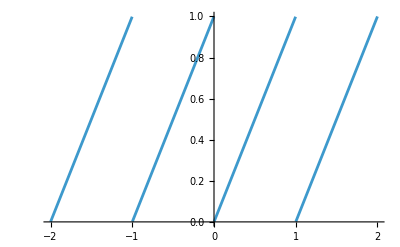

```mathematica
Plot[x - Floor[x], {x, -2, 2}]
```

```mathematica
(*Find the n-th prime number:
Prime[n]*)
```

```mathematica
Prime[4]
```

7

```mathematica
(*Check if x is prime:
PrimeQ[x]*)
```

```mathematica
PrimeQ[11]
```

True

```mathematica
PrimeQ[12]
```

False

```mathematica
(*Prime decomposition of x:
FactorInteger[x]*)
```

```mathematica
FactorInteger[12]
```

{{2,2},{3,1}}

```mathematica
(*Greatest Common Divisor of a and b:
GCD[a, b]*)
```

```mathematica
GCD[10, 25]
```

5

```mathematica
(*Least Common Multiple of a and b:
LCM[a, b]*)
```

```mathematica
LCM[10, 25]
```

50

```mathematica
(*Find all divisors of x:
Divisors[x]*)
```

```mathematica
Divisors[26]
```

{1,2,13,26}

```mathematica
(*Solve an expression y for x:
Solve[y, x]*)
```

```mathematica
s = Solve[x^2 - 1==x, x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
(*Extract answers of s into a list A*)
```

```mathematica
A=x/.s
```

{1/2 (1-√5),1/2 (1+√5)}

```mathematica
(*Extract element i of a list A:
A[[i]]*)
```

```mathematica
x1=A[[1]]
x2=A[[2]]
```

1/2 (1-√5)

1/2 (1+√5)

```mathematica
s[[1]]
```

{x→1/2 (1-√5)}

```mathematica
s[[1]][[1]]
```

x→1/2 (1-√5)

```mathematica
s[[1]][[1]][[2]]
```

1/2 (1-√5)

```mathematica
(*Maximum Value of a List*)
```

```mathematica
A={2, 4, -1, 7, 3}
```

```mathematica
d=Length[A]
```

```mathematica
max=A[[1]]
```

```mathematica
(*Loop with body b and counter i between m and n:
Do[b, {i, m, n}]*)
```

```mathematica
(*Condition c with true body t and false body f:
If[c, t, f]*)
```

```mathematica
Do [
If[
A[[i]]>max,
max=A[[i]]
]
, {i, 1, d}
]
```

```mathematica
max
```

7

```mathematica
(*Find the root*)
```

```mathematica
f[x_]=x-Cos[x]
```

```mathematica
(*Differential of function f(x) with respect to x:
D[f[x], x]*)
```

```mathematica
df[x_]=D[f[x], x]
```

```mathematica
x[0]=0
```

```mathematica
Do[
x[n+1]=x[n]-f[x[n]]/df[x[n]];
Print[N[x[n+1]]],
{n, 0, 10}
]
```

1.

0.750364

0.739113

0.739085

0.739085

0.739085

«5 more identical outputs»

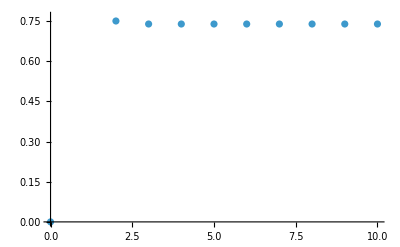

```mathematica
ListPlot[Table[{i, x[i]}, {i, 0, 10}]]
```